# 6

## PHAS2443: Practical Mathematics II Lecture 6: The Wave Equation(s)

The wave equation is found in an enormous number of areas of physics. The classical wave equation, which describes electromagnetic waves, sound waves, elastic waves in solids, and so on, has to be solved for problems with various geometries. Sometimes these are simple (for example, propagation of light down a cylinder for communications systems involving fibre optics) and sometimes complex (sound waves travelling through a metal reinforced with hard particles or fibres, in the context of nondestructive testing, looking for cracks or other mechanical defects in advanced aircraft structures). For the more complicated cases, the use of numerical methods is almost inevitable. Quantum theory, of course, treats all matter as waves (though the equation is different from the classical wave equation), and has the same problems of complicated geometry (atoms in various positions) with the added complication that electrons, for example, interact with each other makes the problem nonlinear.

Crucially, though, although the classical wave equation is a hyperbolic equation, the Schrödinger equation is a parabolic equation. From what we learnt in Lecture 5, this means that the two equations require different boundary equations. At a more profound level, the fact that the characteristic curves of the classical wave equation form a real orthogonal net whilst those of the Shrodinger equation do not, has profound effects on the way information is propagated classically and quantum mechanically.

## Numerical models of the classical wave equation

The wave equation
(∂^2 θ)/(∂t^2) =c^2 (∂^2 θ)/(∂x^2),
is, as mentioned in Lecture 5, a hyperpolic equation. This means that the solution propagates from initial conditions specified by giving θ and ⅆθ/ⅆt for all positions x. A sensible approach is to use a standard finite difference scheme, dividing space and time into equal intervals Δx and Δt and using
(∂^2 θ(i Δx, nΔt))/(∂t^2) = (θ(iΔx, (n+1)Δt)-2θ(iΔx, nΔt)+θ(iΔx,(n-1)Δt))/(Δt)^2 ,
and similarly for the spatial derivative. Substituting and rearranging, we find
θ(iΔx, (n+1)Δt)=2θ(iΔx, nΔt)-θ(iΔx, (n-1)Δt)+((c Δt)/Δx)^2[θ((i+1)Δx, nΔt)-2θ(iΔx, nΔt)+θ((i-1)Δx,nΔt)],
which is an explicit update scheme, giving the field at point in terms of the field at that point at the previous two time-steps and at the neighbouring point at the previous time-step. If you think about the amount of computer storage this needs, you can see that you only need enough memory to store two steps, as you can overwrite the values at (n-1) with those at (n+1) as you calculate them: this is not worth worrying about in one spatial dimension, but for two or three dimensions it becomes important.
You can see that the one parameter that governs the scheme is r=(c Δt)/Δx, called the Courant parameter. The accuracy is improved if we take small steps: the stability is governed by the  value of r. It turns out that for stability, r must be less than or equal to 1, which is called the Courant-Friedrichs-Lewy (CFL) condition. This has an intuitive explanation: the method only takes into account the nearest neighbours of any point in space i: if the time step Δt is so large that the wave can propagate further than Δx during one time step, we cannot expect to model that.
The other point that is clear is that to start the calculation we need the values of the wave field at all points in time at two successive time steps. This sounds different from the Cauchy boundary conditions our analysis in Lecture 5 told us we needed, but it is equivalent (after all, from the two values a backward difference approximation will give us the time derivatives at the second time step).
Let's code this up and check that it behaves the way we expect.  To do the calculation efficiently we will use the Rotate functions: note that this imposes periodic boundary conditions, so that with an array of length N entry N+1 is equivalent to entry 1. 
If we choose to set up a sine wave, at time zero it will have the form
     sin(kx) = sin(i k Δx) 
on the mesh,  but at time Δt it will look like
    sin(k x - ω Δt) = sin(k (i Δx - (ω/k) Δt)
                                   = sin(k Δx (i - c Δt/Δx)) 
                                   = sin (k Δx (i-r))
 We'll set up a sine wave, with a wavelength of 20 points, on a mesh of 100 points:

r=0.9
last=Table[Sin[2 π i/20.],{i,1,100}];
now=Table[Sin[2 π (i-r)/20.],{i,1,Length[last]}];upd[{now_,last_}]:={2now-last+r^2(RotateRight[now]-2 now + RotateLeft[now]),now};
ListPlot[last,Joined→True]
Do[{now,last}=upd[{now,last}],{i,1,10}];
ListPlot[last,Joined→True]

0.9

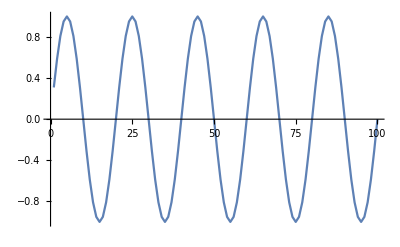

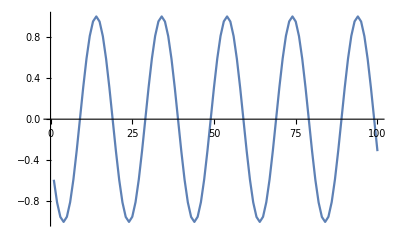

#### Explanation

Start by defining the dimensionless parameter (Courant number) r=c Δt/Δx

```mathematica
r=0.9
```

then set up the sine wave sin(k(x-c t)) with k=2π/(20 Δx). This corresponds to a wavelength 2π/k=20 Δx, giving us 20 points per wavelength, which should be enough to represent the wave accurately. First we set up, in last, the wave at time zero

```mathematica
last=Table[Sin[2 π i/20.],{i,1,100}];
```

and then the wave at time Δt, which is sin(k(x-c Δt)) = sin(k Δx(x/Δx-r))

```mathematica
now=Table[Sin[2 π (i-r)/20.],{i,1,Length[last]}];
```

The update scheme using Rotate functions will result in periodic boundary conditions, wrapping round at the edges of the range.

```mathematica
upd[{now_,last_}]:={2now-last+r^2(RotateRight[now]-2 now + RotateLeft[now]),now}
```

Plot the initial wave-form.

```mathematica
ListPlot[last,Joined->True]
```

Run the update scheme for 10 steps (note that we could have used Nest here)

```mathematica
Do[{now,last}=upd[{now,last}],{i,1,10}];
```

and plot the final wave-form.

```mathematica
ListPlot[last,Joined->True]
```

We can clearly see that the wave has advanced, but we can do better. Let's try to animate our result.

```mathematica
r=0.9
last=Table[Sin[(2 π i)/20.],{i,1,100}];
now=Table[Sin[(2 π (i-r))/20.],{i,1,Length[last]}];ListAnimate[(ListPlot[#1,Joined->True]&)/@Transpose[NestList[upd,{now,last},20]]⟦1⟧]
```

0.9

#### Explanation

We run exactly the same scheme as before, except that by using NestList we make a list of the result at each timestep, which we can plot by Mapping ListPlot onto it.

```mathematica
(ListPlot[#1,Joined->True]&)/@Transpose[NestList[upd,{now,last},20]]⟦1⟧;
```

```mathematica
NestList[upd,{now,last},20]
```

will return the traces in the form {{t0,t1},{t1,t2},{t2,t3}...}, so if we Transpose this we get {{t0,t1,t2...},{t1,t2,t3...}}, Part 1 of which is what we want, {t0,t1,t2...}, and that's what we Map ListPlot onto.

We can show theoretically that this finite difference scheme is stable only for values of r=(c Δt)/Δx≤ 1 (CFL condition).  A simple experiment shows that we do indeed hit problems if we violate this condition (physical intuition tells us that this is reasonable, as our difference scheme only links each point with its nearest neighbours at the next time step so if the time step is large enough for information to travel further than one nearest neighbour distance in one time step we can expect trouble). If we set r=1.01, all looks fine if we only run for 100 time steps, but problems are clearly present by the time we get to 120 steps, and by 150 we are left only with numerical noise.

r=1.01
last=Table[Sin[2 π i/20.],{i,1,100}];
now=Table[Sin[2 π (i-r)/20.],{i,1,Length[last]}];upd[{now_,last_}]:={2now-last+r^2(RotateRight[now]-2 now + RotateLeft[now]),now}
ListPlot[last,Joined→True]
Do[{now,last}=upd[{now,last}],{i,1,150}];
ListPlot[last,Joined→True]

1.01

-Graphics-

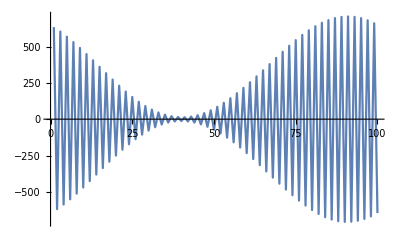

So much for stability. The other point we have to consider is accuracy. Crudely speaking, this boils down to a question of how many points per wavelength we need for a reasonable representation of a waveform. It is pretty clear that four is a minimum, 10 is getting there, and 20 is quite good:

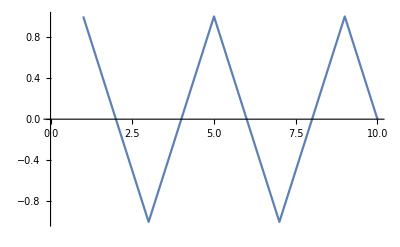

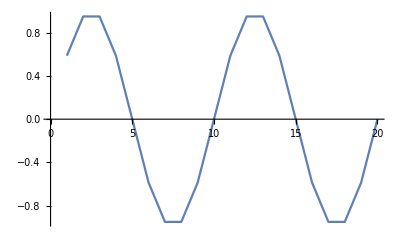

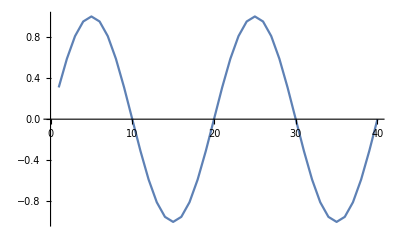

```mathematica
ListPlot[Table[Sin[(2 π i)/4.],{i,1,10}],Joined->True]
ListPlot[Table[Sin[(2 π i)/10.],{i,1,20}],Joined->True]
ListPlot[Table[Sin[(2 π i)/20.],{i,1,40}],Joined->True]
```

So we expect to need to use about 20 points per wavelength to describe the wave properly. What happens if we have too few points? We can see that the wave still propagates, and stays wave-like.

r=0.9
last=Table[Sin[2 π i/4.],{i,1,12}];
now=Table[Sin[2 π (i-r)/4.],{i,1,Length[last]}];upd[{now_,last_}]:={2now-last+r^2(RotateRight[now]-2 now + RotateLeft[now]),now}
ListPlot[last,Joined→True]
Do[{now,last}=upd[{now,last}],{i,1,10}];
ListPlot[last,Joined→True]

0.9

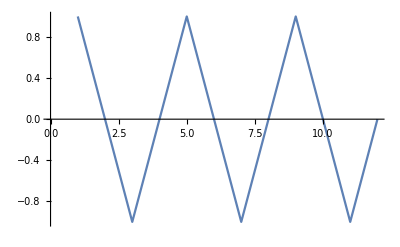

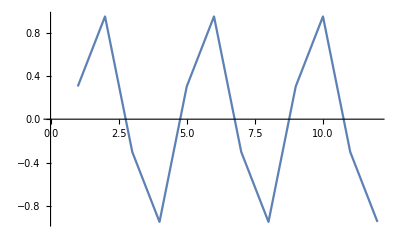

If we compare a coarse discretisation with a finer one, though, we can see a problem (here we need to alter the form of the data we feed to ListPlot, to get both curves plotted on the same axes).  By varying the time for which we run the calculation (ttot) and hence the number of timesteps we take (stps in the code below) we can see that the more crudely discretised wave has a different phase velocity from the more finely discretised one.  Note that to keep the same r value a shorter Δx requires more timesteps to reach a given final time. The wave speed is 1 and the wavelength is 1, so in a total time of 9 it should have moved forwards by 9 wavelengths.

r=0.9;ttot=9.001;
Δx=.25;
stps=Floor[ttot/(r Δx)];
last=Table[Sin[2 π i Δx],{i,1,Floor[3.001/Δx]}];
p10=ListPlot[Transpose[{Table[i Δx,{i,1,Length[last]}],last}],Joined→True,PlotStyle→RGBColor[1,0,0],PlotLabel->"Red: initial
Blue: final"];
now=Table[Sin[2 π Δx(i-r)],{i,1,Length[last]}];upd[{now_,last_}]:={2now-last+r^2(RotateRight[now]-2 now + RotateLeft[now]),now}
Do[{now,last}=upd[{now,last}],{i,1,stps}];
p1=ListPlot[Transpose[{Table[i Δx,{i,1,Length[last]}],last}],Joined→True];
Δx=.0625;
stps=Floor[ttot/(r Δx)];
last=Table[Sin[2 π i Δx],{i,1,Floor[3.001/Δx]}];
p20=ListPlot[Transpose[{Table[i Δx,{i,1,Length[last]}],last}],Joined→True,PlotStyle→RGBColor[1,0,0]];
now=Table[Sin[2 π  Δx(i-r)],{i,1,Length[last]}];upd[{now_,last_}]:={2now-last+r^2(RotateRight[now]-2 now + RotateLeft[now]),now}
Do[{now,last}=upd[{now,last}],{i,1,stps}];
p2=ListPlot[Transpose[{Table[i  Δx,{i,1,Length[last]}],last}],Joined→True];
Show[p10,p1,p20,p2]
Δx=.;r=.;ttot=.;stps=.;

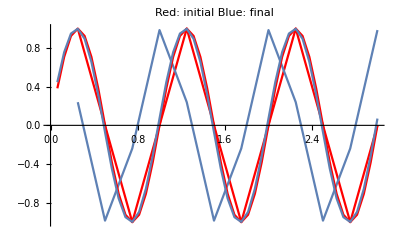

#### Explanation

Set up the time we want to model: making it slightly more than 9 and using the Floor function makes sure that we get the right number of steps despite possible rounding errors when using real numbers.

```mathematica
r=0.9;ttot=9.001;
```

Choose a step size in space, and use Δt=r Δx/c with c=1 to calculate the number of time steps needed.

```mathematica
Δx=.25;
stps=Floor[ttot/(r Δx)];
```

Set up the wave at times 0 and Δt, and plot the initial wave (in red).

```mathematica
last=Table[Sin[2 π i Δx],{i,1,Floor[3.001/Δx]}];
p10=ListPlot[Transpose[{Table[i Δx,{i,1,Length[last]}],last}],Joined->True,PlotStyle->RGBColor[1,0,0],PlotLabel->"Red: initial\nBlue: final"];
now=Table[Sin[2 π Δx (i-r)],{i,1,Length[last]}];
```

Define the update function, which is the same as we have used before, run for the required number of steps, and plot the final waveform.

```mathematica
upd[{now_,last_}]:={2 now-last+r^2 (RotateRight[now]-2 now+RotateLeft[now]),now}
Do[{now,last}=upd[{now,last}],{i,1,stps}];
p1=ListPlot[Transpose[{Table[i Δx,{i,1,Length[last]}],last}],Joined->True];
```

Repeat with finer discretisation.

```mathematica
Δx=0.0625;
stps=Floor[ttot/(r Δx)];
last=Table[Sin[2 π i Δx],{i,1,Floor[3.001/Δx]}];
p20=ListPlot[Transpose[{Table[i Δx,{i,1,Length[last]}],last}],Joined->True,PlotStyle->RGBColor[1,0,0]];
now=Table[Sin[2 π Δx (i-r)],{i,1,Length[last]}];upd[{now_,last_}]:={2 now-last+r^2 (RotateRight[now]-2 now+RotateLeft[now]),now}
Do[{now,last}=upd[{now,last}],{i,1,stps}];
p2=ListPlot[Transpose[{Table[i Δx,{i,1,Length[last]}],last}],Joined->True];
```

Put all the plots together with Show,

```mathematica
Show[p10,p1,p20,p2]
```

and finally clear a few variables.

```mathematica
Δx=.;r=.;ttot=.;stps=.;
```

What this illustrates is the phenomenon of grid dispersion. For a given spatial grid, different frequencies will propagate at different speeds. This means that in general signal pulses, which are composed of a variety of different frequencies, will be distorted as they pass through the grid. Any real calculation is a compromise between accuracy and computation time.

Although we have only treated the one-dimensional wave equation here, similar finite difference schemes can be developed in two and three dimensions. Here, for example, is a wave in two dimensions scattering from a solid cylinder.  We again use a second order difference scheme with explicit time-stepping. The initial wave is set up as a sinusoidal pulse, smoothed at the ends of the wavefront, and chopped at front and rear.

Clear["Global`*"]
dimx=100;dimy=100;
mesh=Table[0.,{j,1,dimy},{i,1,dimx}];vel=1;dx=1;dt=.7;
prev=mesh;ϵ=vel^2 dt^2/dx^2;smear=1.;λ=20;
ϵ
xpos=dimx/7;xwid=λ;
Do[mesh[[j,i]]=Sin[2 π (i-xpos) dx/λ]/((1+Exp[-(j- dimy/8)/smear])(1+Exp[-(7 dimy/8-j)/smear]));prev[[j,i]]=Sin[(2 π /λ)((i-xpos) dx + vel dt)]/((1+Exp[-(j- dimy/8)/smear])(1+Exp[-(7 dimy/8-j)/smear])),{j,1,dimy},{i,Floor[xpos-xwid/2],Floor[xpos+xwid/2]}];
ss[c_]:=Hue[(c+2)/5]
d=5
bc[]:=Do[mesh[[j,i]]=0,{j,dimy/2-d,dimy/2+d},{i,dimx/2-d,dimx/2+d}]
dbc[]:=Do[mesh[[j,1]]=0;mesh[[j,dimx]]=0,{j,1,dimy}];
pbc[]:=Do[prev[[j,i]]=0,{j,dimy/2-d,dimy/2+d},{i,dimx/2-d,dimx/2+d}]
pdbc[]:=Do[prev[[j,1]]=0;mesh[[j,dimx]]=0,{j,1,dimy}];Do[mesh[[1,i]]=0;mesh[[dimy,i]]=0,{i,1,dimx}];
bc[];pbc[];
dbc[];pdbc[];
ListDensityPlot[mesh,Mesh→False,ColorFunctionScaling→False,ColorFunction→ss,AspectRatio→Automatic,PlotLabel->"Initial Wave"]

0.49

5

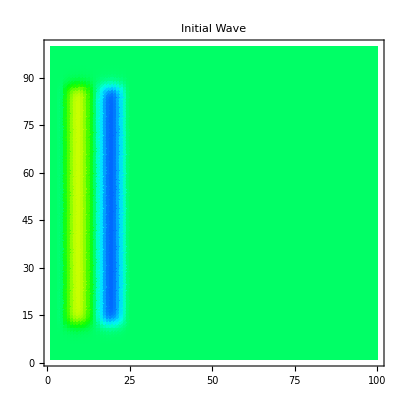

#### Explanation

Start by cleaning up memory, defining the dimensions of the mesh, and setting the mesh to zero.

```mathematica
Clear["Global`*"]
dimx=100;dimy=100;
mesh=Table[0.,{j,1,dimy},{i,1,dimx}];
```

Then define a wave speed, space and time steps, and the initial wave which is a sine function in the x direction, centred on x=xpos and of length xwid. In the y direction the wave is smoothly reduced in amplitude, with an exponential with a width governed by smear.

```mathematica
vel=1;dx=1;dt=.7;
prev=mesh;
ϵ=vel^2 dt^2/dx^2;
smear=1.;λ=20;
xpos=dimx/7;xwid=λ;
Do[mesh[[j,i]]=Sin[2 π (i-xpos) dx/λ]/((1+Exp[-(j- dimy/8)/smear])(1+Exp[-(7 dimy/8-j)/smear]));prev[[j,i]]=Sin[(2 π /λ)((i-xpos) dx + vel dt)]/((1+Exp[-(j- dimy/8)/smear])(1+Exp[-(7 dimy/8-j)/smear])),{j,1,dimy},{i,Floor[xpos-xwid/2],Floor[xpos+xwid/2]}];
```

As the standard colour function used in ListDensityPlot has the rather confusing effect of colouring the maximum and minimum values the same, define a modified function.

```mathematica
ss[c_]:=Hue[(c+2)/5]
```

bc[] sets zero values for the field on a square scatterer 2d by 2d in the middle of the mesh for the field at the current time step. If we take the field to be the magnitude of the displacement in an acoustic wave, that would correspond to a square rigid body at that position.

```mathematica
d=5
bc[]:=Do[mesh[[j,i]]=0,{j,dimy/2-d,dimy/2+d},{i,dimx/2-d,dimx/2+d}]
```

dbc[] sets zero values on the left and right boundaries for the current step: this would correspond to having our wave travelling down a channel with rigid walls.

```mathematica
dbc[]:=Do[mesh[[j,1]]=0;mesh[[j,dimx]]=0,{j,1,dimy}];
```

pbc[] sets zero values for the field on a square scatterer 2d by 2d in the middle of the mesh for the field at the previous time step.

```mathematica
pbc[]:=Do[prev[[j,i]]=0,{j,dimy/2-d,dimy/2+d},{i,dimx/2-d,dimx/2+d}]
```

pdbc[] sets zero values on the upper and lower boundaries at the previous step.

```mathematica
pdbc[]:=Do[prev[[j,1]]=0;mesh[[j,dimx]]=0,{j,1,dimy}];
```

And if you were wondering (and you all were, weren't you?) why I didn't just define bc so that I could pass a set of values to it, as in

```mathematica
bc[mm_]:=Do[mm[[j,i]]=0,{j,dimy/2-d,dimy/2+d},{i,dimx/2-d,dimx/2+d}]
```

the reason is that Mathematica will not let a function alter its arguments. For example

```mathematica
mm={1,2,3}
test[m_]:=(m[[2]]=99)
test[mm]
mm
```

{1,2,3}

Set::setps: {1,2,3} in the part assignment is not a symbol.

99

{1,2,3}

Set the values on the other edges to be zero initially

```mathematica
Do[mesh[[1,i]]=0;mesh[[dimy,i]]=0,{i,1,dimx}];
```

Now apply all the boundary conditions and plot the initial wave, usiing the colour function defined above.

```mathematica
bc[];pbc[];
dbc[];pdbc[];
ListDensityPlot[mesh,Mesh->False,ColorFunctionScaling->False,ColorFunction->ss,AspectRatio->Automatic,PlotLabel->"Initial Wave"]
```

pbc[]sets zero values for the field on a square scatterer 2d by 2d in the middle of the mesh for the field at the previous time step
pdbc[]sets zero values on the upper and lower boundaries at the previous step.

For a bit of variety, we will apply the finite difference operator using a convolution approach rather than by Rotating the matrices. We introduced convolutions in the context of cellular automata in Lecture 2. One of the exercises will ask you to see which approach is faster. The figures are labelled with the time, and the maximum and minimum values of the field in the mesh.

SameSizeConvolve[kernel_,image_]:=Module[{i,trim,dims}, i=ListConvolve[kernel,image,{1,-1}];trim=(Dimensions[kernel]-1)/2; dims=Dimensions[i]; Take[i,{1+trim⟦1⟧, dims⟦1⟧- trim⟦1⟧},{1+ trim⟦2⟧, dims⟦2⟧- trim⟦2⟧}]] 
pint=10;tmax=100;
steps=Floor[tmax/dt];
pst=Floor[pint/dt];
Timing[Do[{prev,mesh}={mesh, SameSizeConvolve[{{0.,ϵ,0.},{ϵ,2-4 ϵ,ϵ},{0.,ϵ,0.}},mesh]-prev};bc[];dbc[];If[Floor[it/pst]==it/pst,Print[ListDensityPlot[mesh,Mesh→False,ColorFunctionScaling→False,ColorFunction→ss,PlotLabel→{it dt,Min[mesh],Max[mesh]},AspectRatio→Automatic]];],{it,1,steps}]]

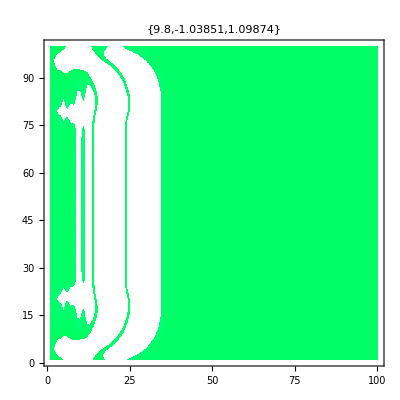

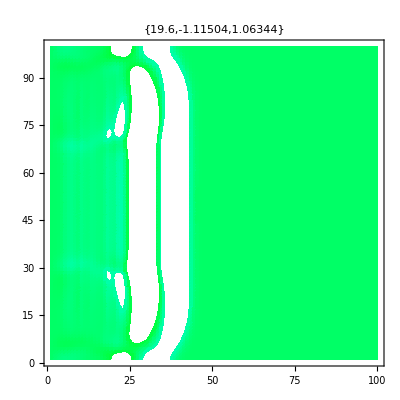

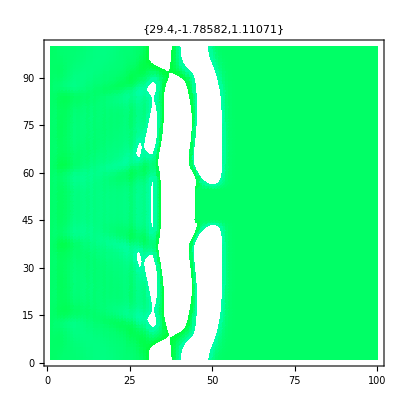

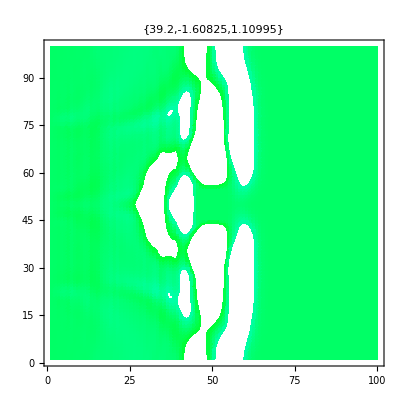

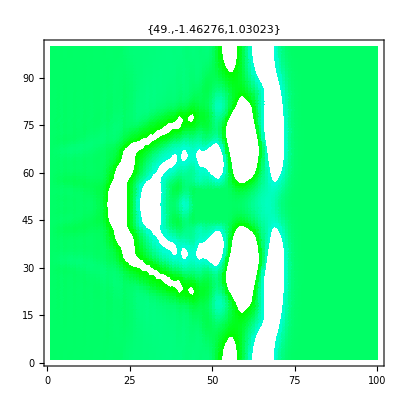

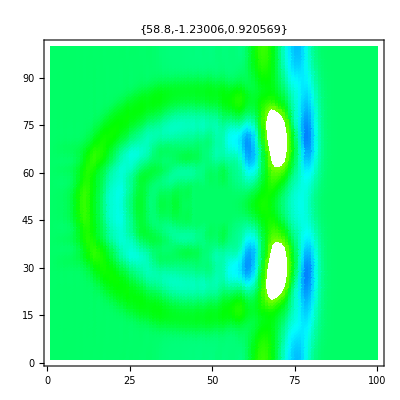

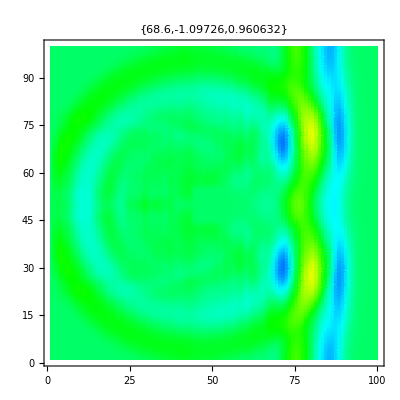

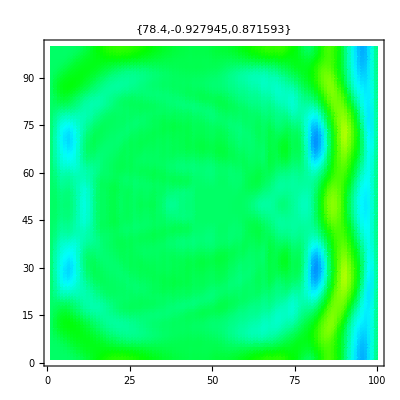

{24.4639,Null}

#### Explanation

The first thing to do is to define a function which will convolve a kernel with a list without altering the dimensions of the list. Although we know that the kernel we want to use has the shape 0 | ϵ | 0
ϵ | 2-4ϵ | ϵ
0 | ϵ | 0, the function is written in a more general way.

```mathematica
SameSizeConvolve[kernel_,image_]:=Module[{i,trim,dims}, i=ListConvolve[kernel,image,{1,-1}]; trim=(Dimensions[kernel]-1)/2; dims=Dimensions[i]; Take[i,{1+trim⟦1⟧, dims⟦1⟧- trim⟦1⟧},{1+ trim⟦2⟧, dims⟦2⟧- trim⟦2⟧}]]
```

When the convolution is first formed with a kernel of dimension 3 by 3 and saved in i, it will have dimensions 2 greater in each dimension than image because of the overhangs at each end (see help file for ListConvolve). By determining the dimensions of kernel and image we can select the central region of i which omits the overhangs, using Take.

Now set the time to run, tmax, and number of time steps, steps. Also arrange to plot at time intervals of pint.

```mathematica
pint=10;tmax=100;
steps=Floor[tmax/dt];
pst=Floor[pint/dt];
Timing[Do[{prev,mesh}={mesh,SameSizeConvolve[{{0.,ϵ,0.},{ϵ,2-4 ϵ,ϵ},{0.,ϵ,0.}},mesh]-prev};bc[];dbc[];If[Floor[it/pst]==it/pst,ListDensityPlot[mesh,Mesh->False,ColorFunctionScaling->False,ColorFunction->ss,PlotLabel->{it dt,Min[mesh],Max[mesh]},AspectRatio->Automatic]],{it,1,steps}]]
```

Note that after each update with
{prev,mesh}={mesh, SameSizeConvolve[{{0.,ϵ,0.},{ϵ,2-4 ϵ,ϵ},{0.,ϵ,0.}},mesh]-prev}
we apply the boundary conditions with
bc[];dbc[]
and plot the results if the time-step it is a multiple of the plotting interval pst.

## Numerical models of the Schrödinger equation

The form of the time-dependent Schrödinger equation is very similar to that of the diffusion equation - in fact, in the 1930s Dirac suggested treating the Schrödinger equation as a diffusion equation with an imaginary time constant. So for a one-dimensional time-dependent Schrödinger equation, the techniques we used for the time-dependent heat equation in Lecture 4 can be applied. Once we go to a steady-state equation, however, the problem in one dimension is analogous to the heated bar with specified end temperatures, and in two or more dimensions the problem is elliptic (involving the Laplacian but no other second derivatives).  We shall look at examples of problems of each type. We shall use atomic units throughout, in which ℏ=1. m_e= 1, and e^2/4 πϵ_0= 1.

### Time-dependent Schrödinger equation in one dimension

In one dimension we can take over directly the numerical methods we used for the heat transfer equations. There is the extra factor that we now have to handle complex numbers, but Mathematica assumes, by default, that all numbers may be complex, so we need to make minimal changes. Let us consider the reflection of a wave packet from a barrier: this is related to the problem you have seen in the Quantum Mechanics course, but there you looked at an infinite sinusoidal wave (and saw the phenomena of standing waves on the incident side of the barrier, transmitted wave on the other side).

  We take a potential which changes smoothly from 0 in |x|>w/2 to V_0  in |x|<w/2:

Clear[w]; Clear[V0]
V[x_]:=V0(Tanh[x+w/2]-Tanh[x-w/2])/4
Plot[V[x]/.w→5/.V0→1,{x,-10,10},PlotRange→All]

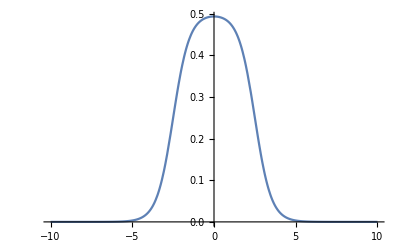

and we want to solve the differential equation (in atomic units)
-1/2 (∂^2 ψ)/(∂x^2)+ V(x) ψ = ⅈ (∂ψ)/(∂t)
with a pulse of input, which we shall write as
 ψ(x,0) = exp(-(x-(x_0))^2/a^2)  exp(ⅈkx).
 If we try to use a simple forward Euler method for the integration (see Lecture 4), we find that the stability condition is upset by the presence of the ⅈ, and the scheme is unconditionally unstable. We have to adopt an implicit scheme: the Crank-Nicholson method is suitable. We will set up the boundary conditions so that ψ goes to zero at the boundaries. This will mean that particles will be reflected from the boundaries as well as from the potential barrier. The easiest way to deal with this is to make the computational region large enough that we can see what is happening at the barrier before any waves reflected from the boundaries get there. There is also a whole science in designing absorbing boundaries, so that numerical simulations can be carried out without any interference from boundary reflections.
 Applying the difference scheme gives
 ⅈ(ψ_(i,n+1)-ψ_(i,n))/Δt=-1/4[(ψ_(i+1,n)-2 ψ_(i,n)+ψ_(i-1,n))/Δx^2+(ψ_(i+1,n+1)-2 ψ_(i,n+1)+ψ_(i-1,n+1))/Δx^2]+1/2[V ψ_(i,n+1)+Vψ_(i,n)],
 giving
  4 ψ_(i,n+1)-ⅈ ζ[ψ_(i+1,n+1)-2 ψ_(i,n+1)+ψ_(i-1,n+1)]+2ⅈ Δt V ψ_(i,n+1)=4 ψ_(i,n)+ⅈ ζ[ψ_(i+1,n)-2 ψ_(i,n)+ψ_(i-1,n)]-2ⅈΔt Vψ_(i,n)
 which we may rewrite in matrix form in the same way as in Lecture 4.  Try running the code below with a barrier height of 0 (to check that the initial pulse propagates freely), 0.5, 1.0 and 2.0. You should see, for the intermediate heights, some trace of resonance within the barrier, so that more than one pulse is reflected.

Δt=0.15;Δx=0.5;ζ= Δt/Δx^2
x0=-50;xmax=100;w=20;V0=1.0;a=5.;k=1;
ψ=Table[Exp[-(x-x0)^2/a^3] Exp[I k x],{x,-xmax,xmax,Δx}];
xi = Table[x,{x,-xmax,xmax,Δx}];
ListPlot[Transpose[{xi,Re[ψ]}],Joined→True,PlotRange→All]
v=Table[V[x],{x,-xmax,xmax,Δx}];
bcl=0;bcr=0;
nx=Floor[2 xmax/Δx]+1;
bvec=2 I ζ Append[Prepend[Table[0,{i,2,nx-1}],bcl],bcr];
mmat=Table[Which[i==j,2(2+I ζ)+2 I Δt v[[i]],i==j+1,- I ζ,i==j-1,- I ζ,True,0],{i,1,nx},{j,1,nx}];
nmat=Table[Which[i==j,2(2-I ζ)-2I Δt v[[i]],i==j+1,I ζ,i==j-1,I ζ,True,0],{i,1,nx},{j,1,nx}];
mmatinv=MatrixPower[mmat,-1];
mmatinvnmat=mmatinv.nmat;
mmatinvbvec=mmatinv.bvec;
step[ψ_List]:=mmatinvbvec+mmatinvnmat.ψ
res=NestList[step,ψ,1000];
Do[Print[ListPlot[Transpose[{xi,Re[res[[i]]]}],Joined→True,PlotRange→All]],{i,1,800,80}]

0.6

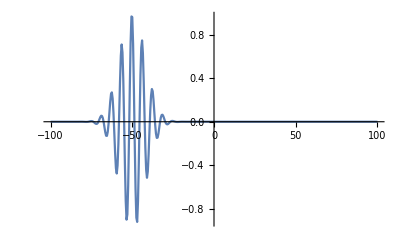

-Graphics-

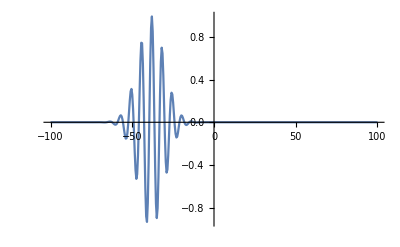

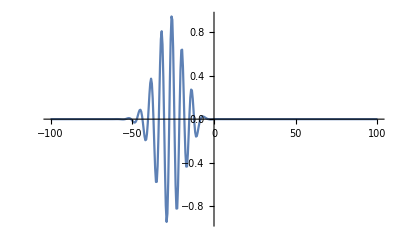

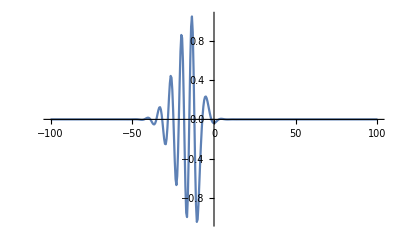

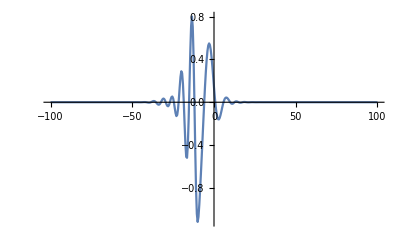

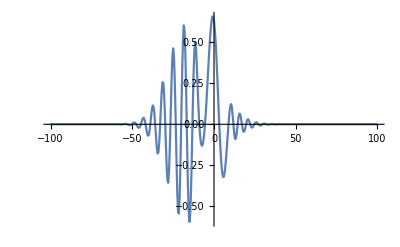

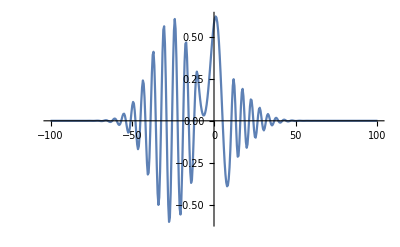

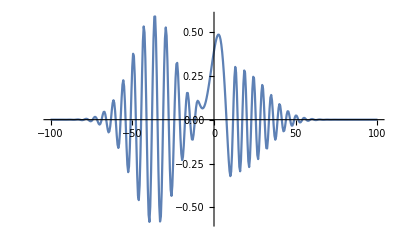

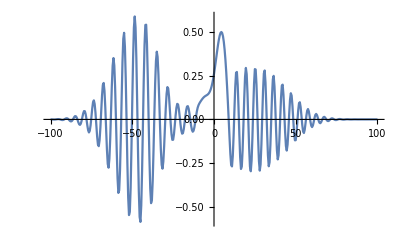

It is worth noting that in these calculations we have been handling 400 by 400 matrices, yet the computation time is tolerable.

#### Explanation

Define constants: time-step, space step, dimensionless parameter ζ (I know it doesn't look dimensionless, but if we undo the conversion to atomic units we'll see it's all right)

```mathematica
Δt=0.15;Δx=0.5;ζ= Δt/Δx^2
```

and constants defining the range of the calculation (-xmax to xmax), the initial pulse centre x0, wavevector k and width a, and the potential barrier height V0 and width w.

```mathematica
x0=-50;xmax=100;w=20;V0=1.0;a=5.;k=1;
```

Set up and plot the initial pulse on the mesh (as it's a complex wavefunction we have to plot either the real or the imaginary part)

```mathematica
ψ=Table[ⅇ^(-(x-x0)^2/a^3) ⅇ^(ⅈ k x),{x,-xmax,xmax,Δx}];
ListPlot[Re[ψ],Joined->True,PlotRange->All]
```

Set up the potential barrier.

```mathematica
v=Table[V[x],{x,-xmax,xmax,Δx}];
```

Set up boundary values: we want the wavefunction to be zero at each end of the mesh.

```mathematica
bcl=0;bcr=0;
```

For convenience, define an integer giving the number of mesh points, nx.

```mathematica
nx=Floor[2 xmax/Δx]+1;
```

Now we start to set up the nx equations, working from
  4 ψ_(i,n+1)-ⅈ ζ[ψ_(i+1,n+1)-2 ψ_(i,n+1)+ψ_(i-1,n+1)]+2ⅈ Δt V ψ_(i,n+1)=4 ψ_(i,n)+ⅈ ζ[ψ_(i+1,n)-2 ψ_(i,n)+ψ_(i-1,n)]-2ⅈΔt Vψ_(i,n)
 or
   (4+2ⅈ ζ +2ⅈ Δt V) ψ_(i,n+1)-ⅈ ζ ψ_(i+1,n+1)-ⅈ ζ ψ_(i-1,n+1)=(4-2ⅈ ζ-2ⅈΔt V) ψ_(i,n)+ⅈ ζ ψ_(i+1,n)+ⅈ ζψ_(i-1,n).
 We write the left-hand side as a matrix mmat multiplying  ψ at time-step n+1, the right-hand side as nmat times ψ at time-step n. It is clear that each matrix has only diagonal terms. The boundary conditions mean that, for example, in the first of the nx equations we have
   (4+2ⅈ ζ +2ⅈ Δt V) ψ_(1,n+1)-ⅈ ζ ψ_(2,n+1)-ⅈ ζ ψ_(0,n+1)=(4-2ⅈ ζ-2ⅈΔt V) ψ_(1,n)+ⅈ ζ ψ_(2,n)+ⅈ ζψ_(0,n),
  but point 0 is not one of the points for which we are solving, so we write the equations with the constant value of ψ at 0,
   (4+2ⅈ ζ +2ⅈ Δt V) ψ_(1,n+1)-ⅈ ζ ψ_(2,n+1)=(4-2ⅈ ζ-2ⅈΔt V) ψ_(1,n)+ⅈ ζ ψ_(2,n)+2ⅈ ζψ_0,
  giving a constant term on the right. This, and the corresponding term from the last point, are the only entries in the boundary condition vector bvec.

```mathematica
bvec=2I ζ Append[Prepend[Table[0,{i,2,nx-1}],bcl],bcr];
mmat=Table[Which[i==j,2(2+I ζ)+2 I Δt v[[i]],i==j+1,- I ζ,i==j-1,- I ζ,True,0],{i,1,nx},{j,1,nx}];
nmat=Table[Which[i==j,2(2-I ζ)-2I Δt v[[i]],i==j+1,I ζ,i==j-1,I ζ,True,0],{i,1,nx},{j,1,nx}];
```

Now we have
   M ψ_(n+1) = N ψ_n + b,
with the solution
   ψ_(n+1) =M^-1 N ψ_n + M^-1 b,
  which we implement in step

```mathematica
mmatinv=MatrixPower[mmat,-1];
mmatinvnmat=mmatinv.nmat;
mmatinvbvec=mmatinv.bvec;
step[ψ_List]:=mmatinvbvec+mmatinvnmat.ψ
```

and now run the calculation using NestList.

```mathematica
res=NestList[step,ψ,1000];
Do[Print[ListPlot[Re[res⟦i⟧],Joined->True,PlotRange->All]],{i,1,800,80}]
```

### Time-independent Schrödinger equation in one dimension

Here we want to solve the equation 
-1/2 (d^2 ψ)/dx^2+ V(x) ψ = E ψ:
the problem is that we will be given boundary conditions on ψ, but we will not know E. Our problem, then, is to find a value or values of E for which we can solve the differential equation subject to the boundary conditions. This is called an eigen value problem. One way of doing this is to use the shooting method which was described in the PHAS1449 course, in Lecture 8.

Let us suppose that we want to find the energy and wavefunction of a particle in a simple harmonic oscillator potential (a problem that can, in fact, be solved exactly),
   V(x) =1/2 k x^2.
What we shall do is to integrate a wavefunction out from x=0 to a large value of x, and insist that the wavefunction goes smoothly to zero at large x. Now to integrate out from  x=0 we need both a value of ψ and a value of the gradient at 0. The whole equation is linear, so within an arbitrary constant it does not matter what value we take for ψ (we can correct the overall scale by normalising later), but the slope we choose will determine the physics.  In fact, because the potential is symmetrical, the probability density |ψ|^2 will also be symmetrical, so ψ is either symmetrical or antisymmetrical.  For the symmetrical states, we choose an arbitrary value for ψ at the origin with a zero gradient, whereas for the antisymmetrical we choose ψ(0)=0 and an arbitrary slope.
Although the physics only requires that ψ tends to zero as x tends to infinity, as we are going to take a finite range of x we need to ensure that we do not pick up a zero value of ψ at that cut off range just by having ψ shift there from large positive to large negative values. We shall try to ensure this by applying a condition of small ψ and small dψ/dx at the cutoff.

Clear[ψ];Clear[x];
rmax=10.;
integ[e_Real,x_]:=ψ[x]/.NDSolve[{-0.5 D[ψ[x],{x,2}]+0.5 x^2 ψ[x]==e ψ[x],ψ[0]==1,ψ'[0]==0},ψ[x],{x,0,rmax}][[1]]
bc[e_?NumericQ]:=Sqrt[(integ[e,x]^2 + ((D[integ[e,x],x]))^2)/.x→rmax]
sol=FindRoot[bc[e]==0.0001,{e,0.,1.}]
Plot[Evaluate[integ[e/.sol[[1]],x]],{x,0,rmax}]

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{e→2.5}

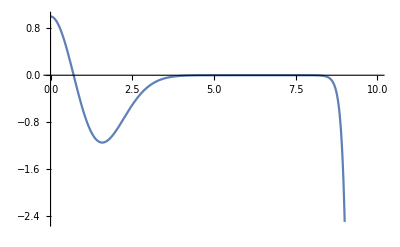

#### Explanation

First set up a fairly simple application of NDSolve: when NDSolve is called the energy e will have a numerical value. Save the result to form a function integ giving the wavefunction.

```mathematica
Clear[ψ];Clear[x];
rmax=10.;
integ[e_Real,x_]:=ψ[x]/.NDSolve[{-0.5 D[ψ[x],{x,2}]+0.5 x^2 ψ[x]==e ψ[x],ψ[0]==1,ψ'[0]==0},ψ[x],{x,0,rmax}][[1]]
```

Define a function to give the square root of the sum of the squares of the function and the derivative at the limit, rmax. As this is going to be used inside FindRoot, insist that e is numerical. Can you see why it may not be enough to insist just that ψ or dψ/dx is zero?

```mathematica
bc[e_?NumericQ]:=Sqrt[(integ[e,x]^2 + ((D[integ[e,x],x]))^2)/.x->rmax]
```

Find the value of energy which satisfies the boundary condition, and plot the result.

```mathematica
sol=FindRoot[bc[e]==0.0001,{e,0.,1.}]
Plot[Evaluate[integ[e/.sol[[1]],x]],{x,0,rmax}]
```

It looks as if we have a sensible wavefunction here, but something is clearly going wrong at large x. We could accept the long flat region as evidence that the function really has converged, and shrug the rest off as numerical noise, or we could explore more closely.

What we can try doing is integrating in the opposite direction. Asymptotically, as x→ ∞, the energy E becomes negligible compared with the potential 1/2 x^2, so the equation takes the form
 (d^2 ψ)/dx^2= x^2 ψ,
which suggests that the asymptotic form of the wavefunction is
ψ(x) →f(x) exp(-x^2/2)
where f(x) is some polynomial in x. We shall try building a solution on that basis: let us assume that the wavefunction goes to zero rather faster than its derivative, and set  arbitrary values at large x. Now, of course, having set the boundary conditions at the large value of x we are trying to integrate inwards to find a zero slope at the origin.

rmax=10.;
integin[e_Real,x_]:=ψ[x]/.NDSolve[{-0.5 D[ψ[x],{x,2}]+0.5 x^2 ψ[x]==e ψ[x],ψ[rmax]==0,ψ'[rmax]==1},ψ[x],{x,0,rmax}][[1]]
bcin[e_?NumericQ]:=Abs[(D[integin[e,x],x])/.x→0.]
sol=FindRoot[bcin[e]==0.0,{e,0.,1.}]
phi0 = (integin[e/.sol[[1]],x])/.x→0.;
dphi0=(D[integin[e/.sol[[1]],x],x])/.x→0.
Plot[Evaluate[integin[e/.sol[[1]],x]/phi0],{x,0,rmax},PlotRange→All]

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{e→2.5}

308544.

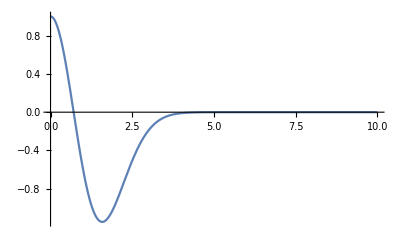

Note that as we set the amplitude of the wavefunction at the outer edge of the range to the arbitrary value of 1, the amplitude close to the origin becomes enormous. The accuracy criterion has not been met in FindRoot, but if we explore the value of ψ and its derivative at the origin we can see that there is no real problem:

```mathematica
phi0
dphi0
```

1.33659×10^18

308544.

The slope being only about 10^-14 times the wavefunction, we can treat this as effectively zero slope. Of course, the large amplitudes will be removed if we normalise the wavefunction.The important point that this illustrates is that it is sometimes better to give a numerical procedure a starting point based on analytic behaviour in some limit than to leave it entirely to its own devices. Sometimes, as here, the behaviour of the function at large range is the clue to give, and sometimes it is useful to look at the expansion of the function near the origin.

## Summary

We have seen how to solve wave equations, both classical and quantum, numerically within Mathematica. There is some more material on quantum methods in the supplementary material on the web, which shows how Mathematica can be used to help with the analytical solution of quantum problems. In the next lecture, however, we shall look at a selection of modelling methods based on particles: from small particles representing atoms, molecules, or other small bits of material to 'particles' as large as planets, stars or galaxies.

A.H. Harker
Physics and Astronomy, UCL
February 2008, revised February 2009, February 2010.
Amended by Patrick Guio, February 2014, February 2015, February 2016, February 2017.

#### Note : Derivation of Second Derivative Expression

We can calculate the finite difference expression for a second derivative as follows: from the Taylor series
   f(x+δx) = f(x) + δx f'(x) + 1/(2!)δx^2 f''(x) + 1/(3!)δx^3 f'''(x) + 1/(4!)δx^4 f''''(x) + O(δx^5) 
   f(x-δx) = f(x) - δx f'(x) + 1/(2!)δx^2 f''(x) - 1/(3!)δx^3 f'''(x) + 1/(4!)δx^4 f''''(x) + O(δx^5)
   and adding these gives
   f(x+δx) +f(x-δx)= 2f(x)  + δx^2 f''(x) + 2/(4!)δx^4 f''''(x) + O(δx^5)
   from which rearrangement gives
   f''(x) = (f(x+δx) +f(x-δx)- 2f(x))/δx^2  - 2/(4!)δx^2 f''''(x) + O(δx^3),
   so that the expression
   f''(x) = (f(x+δx) +f(x-δx)- 2f(x))/δx^2 
   is correct to second order in δx.
   
     One might think of trying to get this result directly from finite difference results that we already know. For example, we could say 
     f''(x) = (f'(x) -f'(x-δx))/δx=((f(x+δx) -f(x))/δx -(f(x) -f(x-δx))/δx)/δx= (f(x+δx) +f(x-δx)- 2f(x))/δx^2 ,                   
     which gives the right answer, but is a bit suspect because we have combined expressions which are only correct to first order (essentially, two first order forward difference schemes) and a lucky cancellation has given us a result correct to second order. 
     Another scheme would be to say
     f''(x) = (f'(x+δx) -f'(x-δx))/(2δx)=((f(x+δx) -f(x))/δx -(f(x) -f(x-δx))/δx)/(2δx)= (f(x+δx) +f(x-δx)- 2f(x))/(2 δx^2),
     and there things go badly wrong because we have combined a hodge-podge of methods, getting the first derivatives with one first-order forward difference scheme and one first-order backward difference scheme, and then getting the second derivative by applying a second-order centred difference scheme to the first derivatives.
     
     A methodical approach is to take centred differences, all with the same spatial step of δx, so that
     f''(x) = (f'(x+δx/2) -f'(x-δx/2))/δx=((f(x+δx) -f(x))/δx -(f(x) -f(x-δx))/δx)/δx= (f(x+δx) +f(x-δx)- 2f(x))/δx^2.
     The result is the same as the first version of combining differences, but the reasoning this time is sound.